# Network Games

## introduction

Un réseaux de jeux G peut représenter des liens sociaux et économiques, et on a l’intention d’étudier l’évolution du réseau qui dépendra des liens créés ou supprimés par les agents ou les
joueurs N qui forment ce réseau.
 On peut faire évoluer le réseau en utilisant un modèle aléatoire où la création et la suppression d’un lien entre deux joueurs (i, j) va être aléatoire sous une certaine probabilité, ou bien en utilisant un modèle stratégique où la création et la suppression des liens entre les joueurs va subir une certaine loi, dans ce modèle, un joueur i peut former un lien avec un autre joueur  j SSI i et j vont en bénéficier de cette relation et aucun des deux ne va perdre, ainsi, i peut supprimer un lien SSI il l’un des deux va bénéficier.
  On va s’intéresser aux modèles stratégiques parce-que les analyses qu’on pourra faire sous ces derniers seront beaucoup plus intéressants.

## Étude théorique

Dans cette section on va essayer de représenter le problème sous sa forme mathématique.

### Notations

N : L’ensemble des noeuds qui représente les joueurs {1, ... , n}.

G(N) : L’ensemble de tous les graphes qu’on peut construire en utilisant les noeuds dans N.

A : L’ensemble des arêtes qui représentent les connexions entre les joueurs A ⊂ N × N.

g : Le graphe qui représente le réseau de jeu.

\[Delta]paclet:ref/character/Delta : Un paramètre qu’on utilisera pour calculer le gain d’un joueur \[Delta]paclet:ref/character/Delta ∈  [0,1].

ℭ : Un paramètre utilisée  pour calculer le coût de formation d’un lien pour un joueur.

μ_i(g) : La fonction de gain d’un noeud i dans le graphe g.

d_(i→j)(g) : La distance de i vers j dans le graphe g.

α_i(g) : c’est le nombre de connexions qui dispose i  dans g (le Degree).

### Fonction de gain

Elle définit le gain d’un joueur dans un graphe g ∈ G(N) ,  μ_i(g)   :  G(N) ↦   ℝ

μ_i(g)  = ∑_(j ∈ N, i \[NotEqual]paclet:ref/character/NotEqual j) (\[Delta]paclet:ref/character/Delta)^(d_(i→j)(g))- ℭ \[CenterDot]paclet:ref/character/CenterDotα_i(g)

### L’évolution du réseau de jeu

Notre but est d’étudier l’évolution du réseau de jeu en fonction du temps, plus précisément la création et la disparition des connexions entre les joueurs jusqu’à ce qu’on obtient un réseau stable, dans cette section on va décrire la manière avec laquelle deux noeuds i et j vont créer ou supprimer une connexion entre eux en utilisant la fonction de gain μ.

#### Création d’une connexion

Deux noeuds i et j vont crée une connexion ⟺ i et j vont bénéficier tous les deux et aucun ne va perdre ⟺  μ_i(⟨V(g),E(g) ∪ {i<->j}⟩)  \[GreaterEqual]paclet:ref/character/GreaterEqual  μ_i(g ) et  μ_j(⟨V(g),E(g) ∪ {i<->j}⟩) \[GreaterEqual]paclet:ref/character/GreaterEqual  μ_j(g)

#### Suppression d’une connexion

Deux noeuds i et j vont supprimer une connexion ⟺ i ou j va bénéficier  ⟺  μ_i(⟨V(g),E(g) ∖ {i<->j}⟩)  >   μ_i(g ) ou  μ_j(⟨V(g),E(g) ∖ {i<->j}⟩) >paclet:ref/character/GreaterEqual μ_j(g), où  μ_-ij est la fonction de gain obtenue par i en supprimant un lien entre i etj.  μ_(+ij) est la fonction de gain obtenue par i en ajoutant  un lien entre i etj.

### La stabilité Fixed-Point

Le réseau se stabilise lorsque aucun noeud ne veut supprimer une connexion et aucun noeud ne veut ou ne peut créer une, c’est le point fixe de l’évolution, c’est la conséquence des actions qui ont été pris par les joueurs qui essaient de poursuivre leurs intérêts personnel.

\[ForAll]paclet:ref/character/ForAll {i<->j} ∈ E, μ_i(⟨V(g),E(g) ∖ {i<->j}⟩))  ≤ μ_i(g ) et μ_i(⟨V(g),E(g) ∖ {i<->j}⟩) ≤ μ_j(g)

\[ForAll]paclet:ref/character/ForAll {i<->j} ∈ E,  μ_i(⟨V(g),E(g) ∪ {i<->j}⟩)  < μ_i(g ) ou μ_i(⟨V(g),E(g) ∪ {i<->j}⟩) < μ_j(g)

### L’Efficacité

Notre projet est d’étudier l’évolution du réseau de jeu, l’efficacité du réseau est une notion trop forte car elle nous permet de valoriser la qualité du réseau et de déterminer si c’est le meilleure réseau à construire car il rapporte un bon bénéfice  global à la société sans tenir compte les intérêts individuels, il tous simplement c’est le meilleur réseau selon le perspective de la société.

Un réseau g est efficace ⟺ \[ForAll]paclet:ref/character/ForAll g'∈G(N) ∑_(i ∈ N) μ_i(g) \[GreaterEqual]paclet:ref/character/GreaterEqual  ∑_(i ∈ N) μ_i(g')

## L’implémentation en Mathematica

### Les paramètres et les variables

On va utiliser dans les fonctions les paramètres et les variables suivants :

#### g : une variable globale qui va contenir tout le temps le réseau.

On va l’initialiser par un graphe qui prend la forme d’une étoile qui a 5 noeud et le noeud 1 est l’intersection des autres noeuds .

```mathematica
c = c= ColorData["Atoms","ColorList"]
colorApply[edge_] := edge->{RandomChoice[c],Thick}
```

{RGBColor[0.65, 0.7, 0.7],RGBColor[0.836713, 1., 1.],RGBColor[0.799435, 0.543572, 0.997559],RGBColor[0.770565, 0.964309, 0.0442359],RGBColor[1., 0.709804, 0.709804],RGBColor[0.4, 0.4, 0.4],RGBColor[0.291989, 0.437977, 0.888609],RGBColor[0.800498, 0.201504, 0.192061],RGBColor[0.578462, 0.85539, 0.408855],RGBColor[0.677263, 0.928423, 0.955287],RGBColor[0.658708, 0.492173, 0.842842],RGBColor[0.628274, 0.850553, 0.0782731],RGBColor[0.8913, 0.631904, 0.627399],RGBColor[0.941176, 0.784314, 0.627451],RGBColor[1., 0.501961, 0],RGBColor[0.90443, 0.97015, 0.13504],RGBColor[0.412698, 0.932689, 0.166398],RGBColor[0.546138, 0.844244, 0.892092],RGBColor[0.534026, 0.420729, 0.705621],RGBColor[0.480072, 0.744591, 0.0955222],RGBColor[0.901961, 0.901961, 0.901961],RGBColor[0.74902, 0.760784, 0.780392],RGBColor[0.65098, 0.65098, 0.670588],RGBColor[0.541176, 0.6, 0.780392],RGBColor[0.611765, 0.478431, 0.780392],RGBColor[0.878431, 0.4, 0.2],RGBColor[0.941176, 0.564706, 0.627451],RGBColor[0.313725, 0.815686, 0.313725],RGBColor[0.784314, 0.501961, 0.2],RGBColor[0.490196, 0.501961, 0.690196],RGBColor[0.800757, 0.542666, 0.533513],RGBColor[0.60508, 0.632465, 0.576489],RGBColor[0.741176, 0.501961, 0.890196],RGBColor[0.917248, 0.657833, 0.0706628],RGBColor[0.58847, 0.22163, 0.16064],RGBColor[0.426019, 0.747462, 0.810413],RGBColor[0.425391, 0.329242, 0.585895],RGBColor[0.325959, 0.646423, 0.095983],RGBColor[0.531014, 1., 1.],RGBColor[0.458599, 0.917466, 0.918573],RGBColor[0.385036, 0.834854, 0.841681],RGBColor[0.310325, 0.752163, 0.769323],RGBColor[0.234466, 0.669394, 0.701499],RGBColor[0.157459, 0.586546, 0.638209],RGBColor[0.0793033, 0.50362, 0.579453],RGBColor[0., 0.420615, 0.525231],RGBColor[0.752941, 0.752941, 0.752941],RGBColor[1., 0.85098, 0.560784],RGBColor[0.728371, 0.440594, 0.422196],RGBColor[0.39799, 0.491477, 0.495586],RGBColor[0.619608, 0.388235, 0.709804],RGBColor[0.816706, 0.451332, 0.0100947],RGBColor[0.580392, 0, 0.580392],RGBColor[0.316906, 0.638078, 0.710252],RGBColor[0.332803, 0.217712, 0.483666],RGBColor[0.165935, 0.55605, 0.0796556],RGBColor[0.928084, 0.716075, 0.329427],RGBColor[0.894824, 0.731424, 0.325131],RGBColor[0.86523, 0.707999, 0.315261],RGBColor[0.837836, 0.662974, 0.301635],RGBColor[0.811992, 0.607859, 0.285626],RGBColor[0.787563, 0.549894, 0.268279],RGBColor[0.764628, 0.493261, 0.250405],RGBColor[0.743177, 0.440115, 0.23269],RGBColor[0.72281, 0.39143, 0.215783],RGBColor[0.702434, 0.347663, 0.200392],RGBColor[0.679962, 0.309234, 0.187368],RGBColor[0.652012, 0.276823, 0.17779],RGBColor[0.613603, 0.251489, 0.173042],RGBColor[0.557855, 0.234598, 0.17489],RGBColor[0.475685, 0.227573, 0.18555],RGBColor[0.781537, 0.717388, 0.716579],RGBColor[0.734443, 0.544489, 0.683471],RGBColor[0.681179, 0.360409, 0.63675],RGBColor[0.605181, 0.367584, 0.556343],RGBColor[0.521806, 0.382125, 0.469204],RGBColor[0.445624, 0.373159, 0.399069],RGBColor[0.815686, 0.815686, 0.878431],RGBColor[1., 0.819608, 0.137255],RGBColor[0.721569, 0.721569, 0.815686],RGBColor[0.65098, 0.329412, 0.301961],RGBColor[0.341176, 0.34902, 0.380392],RGBColor[0.619608, 0.309804, 0.709804],RGBColor[0.670588, 0.360784, 0],RGBColor[0.458824, 0.309804, 0.270588],RGBColor[0.218799, 0.516091, 0.591608],RGBColor[0.25626, 0.0861372, 0.398932],RGBColor[0., 0.473472, 0.04654],RGBColor[0.322042, 0.71693, 0.988479],RGBColor[0.3608, 0.67166, 0.943003],RGBColor[0.397469, 0.628, 0.898853],RGBColor[0.43205, 0.58595, 0.856029],RGBColor[0.464542, 0.54551, 0.814532],RGBColor[0.494945, 0.506679, 0.774361],RGBColor[0.52326, 0.469458, 0.735517],RGBColor[0.549486, 0.433847, 0.697999],RGBColor[0.573624, 0.399845, 0.661808],RGBColor[0.595673, 0.367454, 0.626942],RGBColor[0.615633, 0.336672, 0.593404],RGBColor[0.633505, 0.307499, 0.561191],RGBColor[0.649288, 0.279937, 0.530305],RGBColor[0.662982, 0.253984, 0.500746],RGBColor[0.674588, 0.22964, 0.472513],RGBColor[0.684106, 0.206907, 0.445606],RGBColor[0.691534, 0.185783, 0.420025],RGBColor[0.696874, 0.166269, 0.395772],RGBColor[0.700126, 0.148365, 0.372844],RGBColor[0.701289, 0.13207, 0.351243],RGBColor[0.700363, 0.117385, 0.330968],RGBColor[0.697348, 0.10431, 0.31202],RGBColor[0.692245, 0.0928444, 0.294398],RGBColor[0.685054, 0.0829886, 0.278102],RGBColor[0.675773, 0.0747426, 0.263133],RGBColor[0.664405, 0.0681063, 0.249491],RGBColor[0.650947, 0.0630797, 0.237174],RGBColor[0.635401, 0.0596628, 0.226184],RGBColor[0.635401, 0.056628, 0.226184],RGBColor[0.635401, 0.0528, 0.226184]}

```mathematica
g= StarGraph[20,EdgeStyle -> Map[colorApply,EdgeList[g]], VertexStyle->Thread[VertexList[g]->Take[ColorData["Atoms","ColorList"],Length[VertexList[g]]]], VertexSize->0.1]
```

-Graphics-

#### m : le nombre des arrêts

le nombre des arrêts du graphe.

```mathematica
m = EdgeCount[g]
```

19

#### n : Le nombre des noeuds

```mathematica
n = VertexCount[g]
```

20

#### \[Delta]paclet:ref/character/Delta : le paramètre qu’on utilisera pour calculer le gain d’un joueur \[Delta]paclet:ref/character/Delta ∈ [0,1].

On va prendre \[Delta]paclet:ref/character/Delta = 0.5 dans cet exemple.

```mathematica
δ= 0.5
```

0.5

#### ℭ : le paramètre utilisée pour calculer le coût d’un joueur.

On va prendre ℭ = 1

```mathematica
ℭ = 1
```

1

#### iter : le nombre de fois qu’on veut faire évoluer le graphe

iter est le nombre de pas d’évolution(τ  → τ_(+iter)).

```mathematica
iter = 4
```

4

### Les fonctions

Après la définition des paramètres et des variables on va procéder à la définition des fonctions qu’on va utiliser pour simuler l’évolution du réseau.

#### μ_i(g) : La fonction de gain d’un noeud i dans le graphe g

```mathematica
μ=Function[{g,i}, Sum[Power[δ,GraphDistance[g,i,j]]*Boole[i≠j],{j,1,VertexCount[g]}]-ℭ *VertexOutDegree[g,i]]
```

Function[{g,i},∑_(j=1)^VertexCount[g] δ^GraphDistance[g,i,j] Boole[i≠j]-ℭ VertexOutDegree[g,i]]

Par exemple le gain du noeud 4 est :  0.5 + 2×0.25 -1 = 025

```mathematica
μ[g,4]
```

4.

#### μ_i(⟨V(g),E(g) ∪{i<->j}⟩) : Le gain du joueur i lorsqu’il crée une connexion avec j.

C’est tout simplement le gain de i dans un autre graphe qui est définit par l’ancien graphe plus une arête entre i et j.

```mathematica
SubPlus[μ][g_Graph,i_Integer, j_Integer]:= μ[EdgeAdd[g,i<->j],i]
```

On va calculer le gain que le noeud 4 va avoir lorsqu’il a créé une connexion avec 3.

```mathematica
SubPlus[μ][g,4,3]
```

3.25

#### μ_i(⟨V(g),E(g) ∖ {i<->j}⟩) : Le gain du joueur i lorsqu’il supprime une connexion avec j.

C’est tout simplement le gain de i dans un autre graphe qui est définit par l’ancien graphe moins une arête entre i et j.

```mathematica
SubMinus[μ][g_Graph,i_Integer, j_Integer]:= μ[EdgeDelete[g,i<->j],i]
```

On va calculer le gain que le noeud 4 va avoir lorsqu’il a supprimé une connexion avec 1.

```mathematica
SubMinus[μ][g,4,1]
```

0.

#### L’évolution en utilisant la matrice d’adjacence du graphe

Il’ est clair qu’on a besoin d’une fonction qui va nous permettre de faire évoluer le graphe de l’instant τ  à l’instant τ_(+1), cette fonction prendra en paramètres g_τet retournera g_(τ +_1), on va garder le même principe mais on va utiliser la matrice d’adjacence du graphe g au lieu du graphe lui même car il nous simplifiera le calcule et .
Notre stratégie consiste à appliquer la fonction d’évolution sur la matrice M(g) pour faire avancer l’état du graphe . 
Tous les noeuds à l’instant τ  vont essayer de prendre des actions (création ou rupture de liens) pour augmenter leurs gains à l’instant τ_(+1).

pour1 chaque noeud i ∈ N on prend la ligne de la matrice d'adjacence (M(g))_i 
	pour2 chaque noeud j ∈ N tels que i ≂̸ j
		si (M(g))_ij = 1 (il existe une connexion) et [μ_-ij  >   μ_i(g ) ou  μ_-ji ≥paclet:ref/character/GreaterEqual  μ_j(g) ] 
			alors (M(g))_ij = 0 
		sinon (il n'existe pas une connexion) et [μ_(+ij)  \[GreaterEqual]paclet:ref/character/GreaterEqual  μ_i(g ) et  μ_(+ji) \[GreaterEqual]paclet:ref/character/GreaterEqual  μ_j(g)] 
			alors (M(g))_ij = 1
	fin pour 2
fin pour 1

#### Ajouter une connexion :

La fonction qui va nous permette de savoir si on va ajouter une connexion entre deux noeuds i et j dans le graphe g en testant si la proposition :  μ_i(⟨V(g),E(g) ∪ {i<->j}⟩)  \[GreaterEqual]paclet:ref/character/GreaterEqual  μ_i(g ) et  μ_j(⟨V(g),E(g) ∪ {i<->j}⟩) \[GreaterEqual]paclet:ref/character/GreaterEqual  μ_j(g)  est vrai ou non.

```mathematica
AddConnection[g_Graph, i_Integer, j_Integer]:=SubPlus[μ][g,i,j] ≥ μ[g,i] &&  SubPlus[μ][g,j,i] ≥ μ[g,j]
```

Par exemple on teste si une connexion entre 4 et 3 doit être créée car tous les deux vont bénéficier.

```mathematica
AddConnection[g,4,3]
```

False

#### Supprimer une Connexion

La fonction qui va nous permette de savoir si on va supprimer une connexion entre deux noeuds i et j dans le graphe g en testant si la proposition : μ_i(⟨V(g),E(g) ∖ {i<->j}⟩)  >   μ_i(g ) ou  μ_j(⟨V(g),E(g) ∖ {i<->j}⟩) >paclet:ref/character/GreaterEqual μ_j(g)  est vraie ou non.

```mathematica
DeleteConnection[g_Graph, i_Integer, j_Integer]:=SubMinus[μ][g,i,j] > μ[g,i] ||  SubMinus[μ][g,j,i] > μ[g,j]
```

Par exemple on teste si la connexion entre 4 et 1 doit être supprimée car l’un des deux va bénéficier.

```mathematica
DeleteConnection[g,4,1]
```

True

#### La fonction d’évolution d’une cellule

La fonction qui avance l’état d’un élément de la matrice (M(g))_ij de l’instant τ  à l’instant τ_(+1). Cette fonction prendra en entrée deux arguments :

m : la valeur de l’élément de la matrice M(g), m= (M(g))_ij= 0 ou 1

l : une liste qui contient les indices i et j de  l’élément (M(g))_(ij,) l={i,j}

```mathematica
CellEvolution[m_Integer,l_List]:= If[ m==1,Boole[ ¬DeleteConnection[ g,l[[1]] ,l[[2]] ]] ,Boole[ AddConnection[ g,l[[1]] , l[[2]]] ] ]
```

Par exemple (M(g))_14=1 car il existe une connexion entre 1 et 4, or 1 va bénéficier quand il va supprimer cette connexion, donc la nouvelle valeur de  (M(g))_14 doit être 0.

```mathematica
CellEvolution[1,{1,4}]
```

0

#### La fonction d’évolution de la matrice d’adjacence

La fonction qui avance l’état  de la matrice M(g) de l’instant τ  à l’instant τ_(+1).

Normal[AdjacencyMatrix[g]] : est la fonction qu’on utilise pour calculer la matrice d’adjacence du graphe g.

```mathematica
MatrixEvolution[g_Graph] := MapIndexed[CellEvolution, Normal[AdjacencyMatrix[g]],{2}]
```

On va appliquer la fonction sur le graphe g et on doit normalement trouver un graphe vide car 1 il est entrain de perdre tout ses connexions

```mathematica
MatrixEvolution [g]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

#### La fonction d’évolution du graphe

La dernière fonction est la fonction qui fait évoluer le graphe de l’instant τ  à l’instant τ_(+1).

AdjacencyGraph[M(g)] : est une fonction qui transforme la matrice d’adjacence M(g) en un graphe g’.

```mathematica
Evolution[ga_Graph] := g=AdjacencyGraph[MatrixEvolution[g=ga]]
```

On va appliquer cette fonction pour visualiser le graphe.

```mathematica
Evolution[g]
```

-Graphics-

#### La fonction ListEvolution

Cette fonction permet d’obtenir la liste des graphes lorsqu’on applique la fonction d’évolution iter fois.

```mathematica
EvolutionList[g_Graph,iter_Integer] := NestList[Evolution,g ,iter]
```

#### La fonction StabiliteEvolution

La fonction donne le point fixe de l’évolution, c’est à dire le dernier graphe stable .

```mathematica
StabilityEvolution[g_Graph]:=FixedPoint[Evolution,g]
```

#### La fonction Efficacite

C’est la fonction qui calcule l’Efficacité du graphe g. Cette dernière calcul la somme des gains de tout les noeuds du graphe après la fin de l’evolution .
L’éfficacité a pour objectif d’évaluer l’intérêt générale de la société à partir d’un réseau (graphe) .

```mathematica
EfficiencyEvolution[g_Graph ]:= Sum[μ[g,i],{i,1,VertexCount[g]}]
```

## Interface graphique

Dans cette section on va construire une interface graphique qui va nous permettre de tester l’algorithme en utilisent différents paramètres et topologies de graphe . Ceci a pour but d’ extraire des propositions qui caractériserons ce modèle d’évolution,  ainsi il va permettre à l’utilisateur de manipuler l’évolution du réseau pour tester la validité des propositions dans la section “Analyses” .

### Paramétrage

Dans cette partie on peut fixer les valeur des paramètres de la fonction d’évolution.

#### n : Le nombre des noeuds

Le nombre de noeuds du graphe qu’on veut construire, (8 Par défaut).

```mathematica
Manipulate[n=NodesNumber,{{NodesNumber,8,"n"},1,100,1}]
```

#### m: le nombre des arêtes

Le nombre des arêtes du graphe qu’on veut construire (uniquement pour le graphe aléatoire), il faut que 2\[CenterDot]paclet:ref/character/CenterDotn \[GreaterEqual]paclet:ref/character/GreaterEqual m

```mathematica
Manipulate[m=EdgeNumber,{{EdgeNumber,7,"m"},1,200,1}]
```

#### \[Delta]paclet:ref/character/Delta : Fixer le paramètre qu’on utilisera pour calculer le gain d’un joueur \[Delta]paclet:ref/character/Delta ∈ [0,1].

```mathematica
Manipulate[δ=delta,{{delta,0.5,"δ"},0,1,0.05}]
```

#### ℭ : Fixer le paramètre utilisée pour calculer le coût d’un joueur.

```mathematica
Manipulate[ℭ=cost ,{{cost ,1,"ℭ"},0,5,0.1}]
```

#### g : Le graphe

La topologie du graphe initial qu’on veut construire pour le faire évoluer (par défaut c’est un graphe complet) [parfois il y a des bugs il faut initialiser n et m et ré-exécuter].

```mathematica
Manipulate[g=HighlightGraph[graph,EdgeStyle -> Map[colorApply,EdgeList[graph]], VertexStyle->Thread[VertexList[graph]->Take[ColorData["Atoms","ColorList"],Length[VertexList[graph]]]], VertexSize->0.05],{{graph,CompleteGraph[n],"g"},{CompleteGraph[n]->"Graph Complet",StarGraph[n]->"Graphe étoile",RandomGraph[{n,m}]->"Graphe Aléatoire",CycleGraph[n]->"Graphe cyclique",GridGraph[{IntegerPart[√n]+1,IntegerPart[√n]+1}] ->"Grille",KnightTourGraph[m,n] -> "Graphe cheval d'échec",WheelGraph[n] -> "graphe roue", PetersenGraph[IntegerPart[n/2],3]-> "Graphe de petersen",CirculantGraph[n,{}]->"Graphe vide"},ControlType->PopupMenu}]
```

Take::take: Cannot take positions 1 through 864 in ….

#### iter : le nombre de fois qu’on veut faire évoluer le graphe

Le nombre de fois qu’on veut appliquer la fonction Evolution sur le graphe, c’est le nombre d’itération de la fonction NestList.(τ  → τ_(+iter))

```mathematica
Manipulate[iter=iteration ,{{iteration ,10,"iter"},1,200,1}]
```

#### L : la liste des graphes qui représente les pas d’évolutions du graphe

#### P : Le graphe stable de l’évolution

#### La liste d’évolution

L’animation de l’ensemble des graphes qu’on a obtenue lorsqu’on a appliquer Evolution iter fois.

```mathematica
gifEvolution =ListAnimate[L=EvolutionList[g ,iter],0.8]
```

#### L’éfficacité

L’éfficacité en fonction de l’évolution ( il faut lire de gauche à droite).

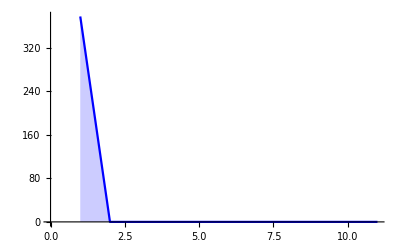

```mathematica
ListLinePlot[Map[EfficiencyEvolution,L],Filling->{1->Axis,2->{1},3->{2}},PlotStyle->{Blue}]
```

#### L’éfficacité accumulée

L’éfficacité accumulé est la somme des gains l’ensemble des joueurs  pour chaque graphe d’évolution, cette somme sera par la suite additionné à la prochaine somme correspondante au prochain graphe jusqu’à la fin.

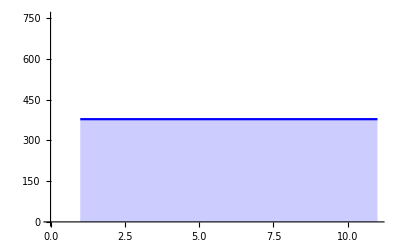

```mathematica
ListLinePlot[Accumulate[Map[EfficiencyEvolution,L]],Filling->{1->Axis,2->{1},3->{2}},PlotStyle->{Blue}]
```

#### La stabilité

Le dernier graphe stable obtenue lors de l’évolution.

```mathematica
P = HighlightGraph[StabilityEvolution[g],EdgeStyle -> Map[colorApply,EdgeList[StabilityEvolution[g]]], VertexStyle->Thread[VertexList[StabilityEvolution[g]]->Take[ColorData["Atoms","ColorList"],Length[VertexList[StabilityEvolution[g]]]]]]
```

-Graphics-

### GIF

On peut aussi exporter la liste d’évolution et le graphe stable sous forme d’une image GIF.

#### L’évolution du réseau

Parfois il prend du temps il faut attendre et il faudra fermer la fenêtre du GIF avant de ré-exécuter cette commande.

```mathematica
SystemOpen[Export["NetworkEvolution.gif",gifEvolution]]
```

#### Le graphe stable

il faut cliquer d’abord exécuter la commande pour obtenir le réseau stable.

```mathematica
SystemOpen[Export["réseau_stable.gif",P]]
```

## Analyses

Dans cette section on va analyser les résultats de la section des tests pour extraire certaines propositions par rapport à l’efficacité et la stabilité du réseau.

### L’efficacité du réseau

On va montrer la structure du réseau efficace que la société (qu’il s’agit d’un ensemble de personnes, entreprises ....) souhaite avoir  lorsqu’on utilise ce modèle d’évolution.

#### Proposition

Le seul réseau efficace qu’on peut avoir en utilisant ce modèle est :

Le réseau représenté par un graphe complet si   (\[Delta]paclet:ref/character/Delta)^2< (\[Delta]paclet:ref/character/Delta)^1 - ℭ

Le réseau représenté par un graphe étoile qui lie tous les noeuds si   (\[Delta]paclet:ref/character/Delta)^1-(\[Delta]paclet:ref/character/Delta)^2<   ℭ < (\[Delta]paclet:ref/character/Delta)^1 + (n-2)/2\[Times]paclet:ref/character/Times(\[Delta]paclet:ref/character/Delta)^2

Le réseau représenté par un graphe vide si   (\[Delta]paclet:ref/character/Delta)^1 + (n-2)/2\[Times]paclet:ref/character/Times(\[Delta]paclet:ref/character/Delta)^2<   ℭ

#### Preuve

Pour la proposition (7) lorsque deux noeuds i et j créent un lien, le gain des autres joueurs du réseau ne diminuent pas et le gain des deux noeuds s’incrémente, car la distance entre i et j va à son tour décrémenter ( puisqu’on a (\[Delta]paclet:ref/character/Delta)^(d_(i→j)(g))≤ (\[Delta]paclet:ref/character/Delta)^1 - ℭ )  , donc le gain global (l’ensemble des joueurs) va augumenter. Par conséquence on aura un graphe complet lorsque le gain global devient maximum.

On va prouver les propositions (8) et  (9)

On commence par prouver que le gain globale d’un graphe qui lie k Noeuds est maximale lorsque le nombre de lien est k-1 (en sachant que le graphe étoile dispose de k-1 liens). Donc le gain d’un graphe qui dispose de k-1 liens est :  2(k-1)((\[Delta]paclet:ref/character/Delta)^1 - ℭ) + (k - 1)(k -2)(\[Delta]paclet:ref/character/Delta)^2( i ), par contre si le nombre de liens m \[GreaterEqual]paclet:ref/character/GreaterEqual k-1,  on aura ((k(k-1))/2 - m)  couple de joueurs qui sont éloignés entre eux d’une distance de 2 au minimum, donc le gain global maximale est :  2m((\[Delta]paclet:ref/character/Delta)^1  ℭ) + (k(k  1)  2m)(\[Delta]paclet:ref/character/Delta)^2 ( ii ).  ( i ) - ( ii ) nous donne  2(m - (k - 1))((\[Delta]paclet:ref/character/Delta)^2-  ((\[Delta]paclet:ref/character/Delta)^1-  ℭ)) qui est positif car  (\[Delta]paclet:ref/character/Delta)^2 >  (\[Delta]paclet:ref/character/Delta)^1-  ℭ et   m \[GreaterEqual]paclet:ref/character/GreaterEqual k-1 .

On va prouver que le graphe qui dispose de k-1 liens et qui a le plus grand gain global est le graphe étoile. Un autre graphe qui a une structure différente du graphe étoile va avoir un gain globale égale à :   2(k - 1)((\[Delta]paclet:ref/character/Delta)^1 -  c) + X , tels que X <  (k -1)(k - 2) (\[Delta]paclet:ref/character/Delta)^2 car deux noeuds au minimum vont avoir une distance plus que 2 entre eux,  donc le gain global de ce graphe sera inférieure au gain global du graphe étoile.

On finira par prouver que le gain global apporté par un seul graphe étoile qui lie tous les noeuds est supérieure au gain rapporté par des sous graphes du graphe étoile.  Soit deux sous graphes étoiles qui contient k_1 et k_2 noeuds respectivement, le gain global du graphe est :  (k_1- 1)[2((\[Delta]paclet:ref/character/Delta)^1-  c) + (k_1-  2)(\[Delta]paclet:ref/character/Delta)^2 ] + (k_2 -  1)[ 2((\[Delta]paclet:ref/character/Delta)^1-  c) + (k_2 -  2)(\[Delta]paclet:ref/character/Delta)^2 ] , ce dernier va être inférieure au gain globale rapporté par le graphe étoile qui contient k_1 + k_2  noeuds :  (k_1 + k_2 -  1)[2((\[Delta]paclet:ref/character/Delta)^1 -  c) + (k_1 + k_2 -  2)(\[Delta]paclet:ref/character/Delta)^2 ]. Donc on conclue que le graphe le plus efficace est le graphe étoile qui contient tous les noeuds ou bien le graphe vide (aucun lien n’existe).

#### Exemple

On prend un exemple pour tester la proposition, δ = 0.5 et ℭ =0.2 on vérifie la condition du proposition (7) et par conséquence le graphe le plus efficace est le graphe complet. On pourra jouer avec les paramètres pour vérifier la validité de la proposition.

```mathematica
Manipulate[δ=delta,{{delta,0.5,"δ"},0,1,0.05}]
```

```mathematica
Manipulate[ℭ=cost ,{{cost ,0.2,"ℭ"},0,5,0.1}]
```

[parfois il y a des bugs il faut initialiser n et m et ré-exécuter]

```mathematica
Manipulate[g=graph,{{graph,CompleteGraph[n],"g"},{CompleteGraph[n]->"Graph Complet",StarGraph[n]->"Graphe étoile",RandomGraph[{n,m}]->"Graphe Aléatoire",CycleGraph[n]->"Graphe cyclique",GridGraph[{IntegerPart[√n]+1,IntegerPart[√n]+1}] ->"Grille",KnightTourGraph[m,n] -> "Graphe cheval d'échec",WheelGraph[n] -> "graphe roue", PetersenGraph[IntegerPart[n/2],3]-> "Graphe de petersen",CirculantGraph[n,{}]->"Graphe vide"},ControlType->PopupMenu}]
```

```mathematica
Dynamic[EfficiencyEvolution[g]]
```

### La stabilité du réseau

On va donner des conjonctures qu’on a déduit à partir des tests sur la stabilité  du réseau  lorsque chaque joueur poursuit ces intérêts personnel, on a pas considérer ces déductions comme des  conclusions et non pas comme des propositions pour la raison d’absence d’un contre exemple ,et pour la raison de la facilitée de démonstration ( c’est presque le même raisonnement des propositions de l’efficacité du réseau).

#### Conjecture

Le réseau représenté par un graphe complet est le seul graphe stable  si   (\[Delta]paclet:ref/character/Delta)^2< (\[Delta]paclet:ref/character/Delta)^1 - ℭ

Le réseau représenté par un graphe étoile est stable ainsi que d'autre topologies peuvent être stable si   (\[Delta]paclet:ref/character/Delta)^1-(\[Delta]paclet:ref/character/Delta)^2<   ℭ < (\[Delta]paclet:ref/character/Delta)^1

Le graphe étoile n'est pas stable par contre les topologies vides et les topologies qui ont beaucoup de connections sont stables   si   (\[Delta]paclet:ref/character/Delta)^1-(\[Delta]paclet:ref/character/Delta)^2<   ℭ < (\[Delta]paclet:ref/character/Delta)^1 + (n-2)/2\[Times]paclet:ref/character/Times(\[Delta]paclet:ref/character/Delta)^2

Le réseau représenté par un graphe vide est le seul graphe stable  si   (\[Delta]paclet:ref/character/Delta)^1 + (n-2)/2\[Times]paclet:ref/character/Times(\[Delta]paclet:ref/character/Delta)^2<   ℭ

#### Remarque

On peut remarquer d’après (8) et (12) qu’un réseau stable n’est pas toujours efficace.

#### Exemple

On prend n=8, δ = 0.5 et ℭ =0.3 pour tester la conjecture (12) et la comparer avec la proposition (8) car d’après la remarque, il semble intéressant d’effectuer cette comparaison.

```mathematica
Manipulate[n=NombreDesNoeuds,{{NombreDesNoeuds,8,"n"},1,100,1}]
```

```mathematica
Manipulate[δ=delta,{{delta,0.5,"δ"},0,1,0.05}]
```

```mathematica
Manipulate[ℭ=cost ,{{cost ,0.3,"ℭ"},0,5,0.1}]
```

[parfois il y a des bugs il faut initialiser n et m et ré-exécuter]

```mathematica
Manipulate[g=HighlightGraph [graph,EdgeStyle -> Map[colorApply,EdgeList[graph]], VertexStyle->Thread[VertexList[graph]->Take[ColorData["Atoms","ColorList"],Length[VertexList[graph]]]], VertexSize->0.1],{{graph,StarGraph[n],"g"},{CompleteGraph[n]->"Graph Complet",StarGraph[n]->"Graphe étoile",RandomGraph[{n,m}]->"Graphe Aléatoire",CycleGraph[n]->"Graphe cyclique",GridGraph[{IntegerPart[√n]+1,IntegerPart[√n]+1}] ->"Grille",KnightTourGraph[m,n] -> "Graphe cheval d'échec",WheelGraph[n] -> "graphe roue", PetersenGraph[IntegerPart[n/2],3]-> "Graphe de petersen",CirculantGraph[n,{}]->"Graphe vide"},ControlType->PopupMenu}]
```

```mathematica
Dynamic[EfficacityEvolution[g]]
```

Donc l’efficacité maximale est 13.3. Par contre lorsqu’on fait évoluer le graphe on remarque que le graphe stable obtenu n’est pas un graphe étoile et son efficacité est inférieur à l’efficacité du graphe étoile 
NB : [parfois il y a des bugs il faut initialiser n et m et ré-exécuter].

```mathematica
Manipulate[g=graph,{{graph,CirculantGraph[n,{}],"g"},{CompleteGraph[n]->"Graph Complet",StarGraph[n]->"Graphe étoile",RandomGraph[{n,m}]->"Graphe Aléatoire",CycleGraph[n]->"Graphe cyclique",GridGraph[{IntegerPart[√n]+1,IntegerPart[√n]+1}] ->"Grille",KnightTourGraph[m,n] -> "Graphe cheval d'échec",WheelGraph[n] -> "graphe roue", PetersenGraph[IntegerPart[n/2],3]-> "Graphe de petersen",CirculantGraph[n,{}]->"Graphe vide"},ControlType->PopupMenu}]
```

```mathematica
ListAnimate[L=EvolutionList[g ,iter],0.8]
```

```mathematica
StabilityEvolution[g]
```

-Graphics-

```mathematica
Dynamic[EfficacityEvolution[g]]
```

## Conclusion

D’après les analyses, un réseau stable n’est pas toujours efficace, cela signifie que si chaque joueur prend des actions en fonction de ces intérêts personnel le réseau obtenue ne sera pas toujours un réseau efficace pour toute la société et donc la meilleure stratégie est de mettre les intérêts personnel à part et investir  sur le développement de la société en coopérant avec les autres (on pourra payer un coût plus grand, on l’occurence, ce coût contribuera à une améloiration).